w+w^2

0.75

-0.25

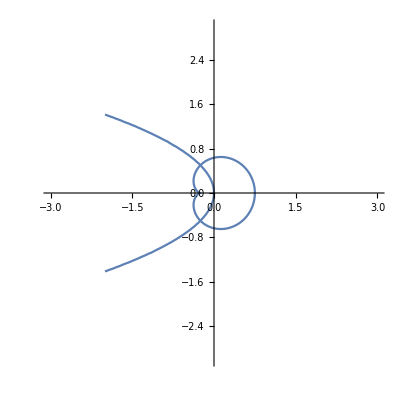

```mathematica
z=(x+I y);
r=.5;
phi[w_]=w+w^2
phi[0.5]
phi[-0.5]
phii[w_]=1/2  *(-1+Sqrt[1+4 w]);
p1=ParametricPlot[{Re[phi[r Exp[I t]]],Im[phi[r Exp[I t]]]},{t,0,2 Pi},PlotRange->{{-3,3},{-3,3}}];
p2=ContourPlot[Abs[(phii[z]-.5)/(phii[z]+.5)]==1.0,{x,-2,2},{y,-2,2}];
Show[p1,p2]
```

{{a→-0.941584},{a→0.280562-0.770961 ⅈ},{a→0.280562+0.770961 ⅈ},{a→0.380461}}

{{a→-0.530008-0.0891036 ⅈ},{a→-0.530008+0.0891036 ⅈ},{a→0.530008-0.74423 ⅈ},{a→0.530008+0.74423 ⅈ}}

0.696905

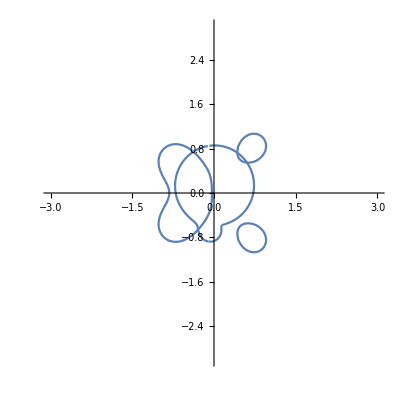

```mathematica
z=(x+I y);



phii[a_]=(a*1.2)^4 + (a*1.2);
Solve[phii[a]- .5== 0, a]
Solve[phii[a]+ .5== 0, a]

Abs[(phii[1I] - .5)/(phii[1I] + .5)]

p1=ParametricPlot[{Re[phi[ Exp[I t]]],Im[phi[ Exp[I t]]]},{t,0,2 Pi},PlotRange->{{-3,3},{-3,3}}];
p2=ContourPlot[Abs[(phii[z]-.5)/(phii[z]+.5)]==1.2,{x,-2,2},{y,-2,2}];
Show[p1,p2]
```

```mathematica
"
```